### Aufgabe 1.1

```mathematica
f[x_,y_]:={E^(1-x)-Cos[y]+0.2,x^2+y-(1+y)x-Sin[x]-0.2}
```

Jacobi-Matrix:

```mathematica
(df[x_,y_]=Transpose[{D[f[x,y], x],D[f[x,y], y]}])//MatrixForm
```

(-ⅇ^(1-x) | Sin[y]
-1+2 x-y-Cos[x] | 1-x)

Jacobi-Matrix im Punkt (1,0)^T:

```mathematica
df[1,0]//MatrixForm
```

(-1 | 0
1-Cos[1] | 0)

Die zweite Spalte ist ein Null-Vektor, daher ist der Rang nicht maximal und somit die Determinante in dem Punkt (1,0)^T null:

```mathematica
Det[df[1,0]]
```

0

Ein zweidimensionales Problem kann gut visualisiert werden. Entsprechend kann ein leicht ein Startpunkt für die drei Lösungen (Schnittpunkte der beiden Kurven blau und orange) gefunden werden.

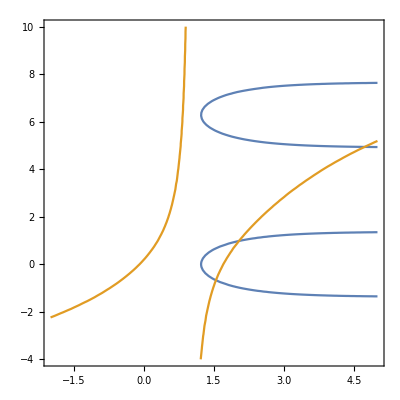

```mathematica
ContourPlot[{f[x,y][[1]]==0,f[x,y][[2]]==0},{x,-2,5},{y,-4,10}]
```

#### Newton-Iteration

1. Punkt: (1.54161,-0.67323)

```mathematica
Norm[df[#[[1]],#[[2]]].#-f[#[[1]],#[[2]]]&[{1,1}],Infinity]
```

0.818227

```mathematica
NestWhileList[#-LinearSolve[df[#[[1]],#[[2]]],f[#[[1]],#[[2]]]]&,{2,-0.5},Norm[f[#[[1]],#[[2]]],Infinity]≥10^-12&]
```

{{2,-0.5},{1.56513,-0.8123},{1.54118,-0.68271},{1.5416,-0.673276},{1.54161,-0.67323},{1.54161,-0.67323}}

2. Punkt: (2.03714,0.983075)

```mathematica
NestWhileList[#-LinearSolve[df[#[[1]],#[[2]]],f[#[[1]],#[[2]]]]&,{2,0.5},Norm[f[#[[1]],#[[2]]],Infinity]≥10^-12&]
```

{{2,0.5},{2.1188,1.23715},{2.03978,0.999024},{2.03717,0.98317},{2.03714,0.983075},{2.03714,0.983075}}

3. Punkt: (4.72363,4.93846)

```mathematica
NestWhileList[#-LinearSolve[df[#[[1]],#[[2]]],f[#[[1]],#[[2]]]]&,{4,4},Norm[f[#[[1]],#[[2]]],Infinity]≥10^-12&]
```

{{4,4},{4.78536,5.14208},{4.71164,4.93064},{4.72361,4.93845},{4.72363,4.93846},{4.72363,4.93846}}

Die Newton-Iteration wird so lange durchgeführt, bis die Gleichung f(x)=0 auf 12 Nachkommastellen erfüllt ist.